## L = 8

```mathematica
arr1={0.88331771,0.95461914,0.95601869, 0.94925830,0.94494783, 0.94477243,0.93989538}
arr2 = {0.89054311, 0.96695181, 0.96867729, 0.96550203, 0.97010479, 0.97021081, 0.96370690}
arr3 = {0.88577527, 0.96578945, 0.96778725, 0.96399909, 0.93126896, 0.93181670, 0.93279545}
arr4={0.88799617, 0.96483383, 0.96886105, 0.96238824, 0.96159325, 0.96127443, 0.95424914}
arr5 ={0.88144669, 0.95870382, 0.96107279, 0.96323384, 0.95990041, 0.95970126, 0.95614453}
```

{0.883318,0.954619,0.956019,0.949258,0.944948,0.944772,0.939895}

{0.890543,0.966952,0.968677,0.965502,0.970105,0.970211,0.963707}

{0.885775,0.965789,0.967787,0.963999,0.931269,0.931817,0.932795}

{0.887996,0.964834,0.968861,0.962388,0.961593,0.961274,0.954249}

{0.881447,0.958704,0.961073,0.963234,0.9599,0.959701,0.956145}

```mathematica
Length[arr1]
```

7

```mathematica
mat = Transpose[{arr1,arr2,arr3,arr4,arr5}]
```

{{0.883318,0.890543,0.885775,0.887996,0.881447},{0.954619,0.966952,0.965789,0.964834,0.958704},{0.956019,0.968677,0.967787,0.968861,0.961073},{0.949258,0.965502,0.963999,0.962388,0.963234},{0.944948,0.970105,0.931269,0.961593,0.9599},{0.944772,0.970211,0.931817,0.961274,0.959701},{0.939895,0.963707,0.932795,0.954249,0.956145}}

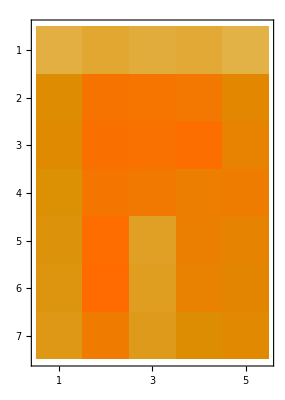

```mathematica
MatrixPlot[mat]
```

```mathematica
n = 7;
yt = Mean[mat[[n]]]
del = StandardDeviation[mat[[n]]]/Sqrt[Length[mat[[n]]]]
```

0.949358

0.00565566

```mathematica
Mean[{0.88331771,0.89054311,0.88577527,0.88799617,0.88144669}]
```

0.885816

```mathematica
mat
```

{{0.883318,0.954619,0.956019,0.949258,0.944948,0.944772,0.939895},{0.890543,0.966952,0.968677,0.965502,0.970105,0.970211,0.963707},{0.885775,0.965789,0.967787,0.963999,0.931269,0.931817,0.932795},{0.887996,0.964834,0.968861,0.962388,0.961593,0.961274,0.954249},{0.881447,0.958704,0.961073,0.963234,0.9599,0.959701,0.956145}}

```mathematica
arr5={0.88331771,0.95461914,0.95601869, 0.94925830,0.94494783, 0.94477243,0.93989538}
arr4= {0.89054311, 0.96695181, 0.96867729, 0.96550203, 0.97010479, 0.97021081, 0.96370690}
arr3 = {0.88577527, 0.96578945, 0.96778725, 0.96399909, 0.93126896, 0.93181670, 0.93279545}
arr4={0.88799617, 0.96483383, 0.96886105, 0.96238824, 0.96159325, 0.96127443, 0.95424914}
arr5 ={0.88144669, 0.95870382, 0.96107279, 0.96323384, 0.95990041, 0.95970126, 0.95614453}
```

```mathematica
mat = Transpose[{arr1,arr2,arr3,arr4,arr5}]
```

### Varia